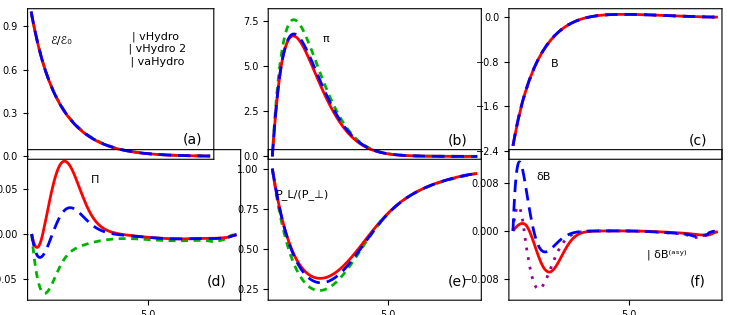
-Graphics-τ (fm/c)

```mathematica
ClearAll["Global`*"]

wd=SetDirectory@NotebookDirectory[];

stylesVH=Directive[RGBColor[0,0,1],AbsoluteThickness[2],AbsoluteDashing[{9,5}]];

stylesVH2=Directive[RGBColor[0,0.7,0],AbsoluteThickness[2],AbsoluteDashing[{5,4}]];

stylesVAH=Directive[RGBColor[1,0,0],AbsoluteThickness[2]];

stylesdB=Directive[RGBColor[0.6,0,0.6],AbsoluteThickness[2],AbsoluteDashing[{2,5}]];


(*//////////////////////////////////////////////////////////////*)

EnergyDensityDataRawVH=Import[wd<>"/eplot_vh.dat"];
piDataRawVH=Import[wd<>"/piplot_vh.dat"];
PiDataRawVH=Import[wd<>"/bulkplot_vh.dat"];
plptDataRawVH=Import[wd<>"/plptplot_vh.dat"];
BDataRawVH=Import[wd<>"/Bplot_vh.dat"];
dB2ndDataRawVH=Import[wd<>"/dB2ndplot_vh.dat"];

EnergyDensityDataVH= Take[EnergyDensityDataRawVH,{2,Length[EnergyDensityDataRawVH]}];
piDataVH= Take[piDataRawVH,{2,Length[piDataRawVH]}];
PiDataVH= Take[PiDataRawVH,{2,Length[PiDataRawVH]}];
plptDataVH= Take[plptDataRawVH,{2,Length[plptDataRawVH]}];
BDataVH= Take[BDataRawVH,{2,Length[BDataRawVH]}];
dB2ndDataVH= Take[dB2ndDataRawVH,{2,Length[dB2ndDataRawVH]}];

energydensityVH = Interpolation[EnergyDensityDataVH[[All,{1,2}]]];
piVH = Interpolation[piDataVH[[All,{1,2}]]];
bulkVH = Interpolation[PiDataVH[[All,{1,2}]]];
plptVH = Interpolation[plptDataVH[[All,{1,2}]]];
BVH = Interpolation[BDataVH[[All,{1,2}]]];
dB2ndVH = Interpolation[dB2ndDataVH[[All,{1,2}]]];



(*//////////////////////////////////////////////////////////////*)


EnergyDensityDataRawVH2=Import[wd<>"/eplot_vh_limit.dat"];
piDataRawVH2=Import[wd<>"/piplot_vh_limit.dat"];
PiDataRawVH2=Import[wd<>"/bulkplot_vh_limit.dat"];
plptDataRawVH2=Import[wd<>"/plptplot_vh_limit.dat"];
BDataRawVH2=Import[wd<>"/Bplot_vh_limit.dat"];
dB2ndDataRawVH2=Import[wd<>"/dB2ndplot_vh_limit.dat"];


EnergyDensityDataVH2= Take[EnergyDensityDataRawVH2,{2,Length[EnergyDensityDataRawVH2]}];
piDataVH2= Take[piDataRawVH2,{2,Length[piDataRawVH2]}];
PiDataVH2= Take[PiDataRawVH2,{2,Length[PiDataRawVH2]}];
plptDataVH2= Take[plptDataRawVH2,{2,Length[plptDataRawVH2]}];
BDataVH2= Take[BDataRawVH2,{2,Length[BDataRawVH2]}];
dB2ndDataVH2= Take[dB2ndDataRawVH2,{2,Length[dB2ndDataRawVH2]}];

energydensityVH2 = Interpolation[EnergyDensityDataVH2[[All,{1,2}]]];
piVH2 = Interpolation[piDataVH2[[All,{1,2}]]];
bulkVH2 =Interpolation[PiDataVH2[[All,{1,2}]]];
plptVH2 = Interpolation[plptDataVH2[[All,{1,2}]]];
BVH2 = Interpolation[BDataVH2[[All,{1,2}]]];
dB2ndVH2 = Interpolation[dB2ndDataVH2[[All,{1,2}]]];


(*//////////////////////////////////////////////////////////////*)
(*NAVIER STOKES*)

PiNSDataRawVH=Import[wd<>"/bulkNSplot.dat"];
PiNSDataVH= Take[PiNSDataRawVH,{2,Length[PiNSDataRawVH]}];
bulkNSVH = Interpolation[PiNSDataVH[[All,{1,2}]]];

piNSDataRawVH=Import[wd<>"/piNSplot.dat"];
piNSDataVH= Take[piNSDataRawVH,{2,Length[piNSDataRawVH]}];
piNSVH = Interpolation[piNSDataVH[[All,{1,2}]]];

piNSDataRawVAH=Import[wd<>"/piNSplot_vah.dat"];
piNSDataVAH= Take[piNSDataRawVAH,{2,Length[piNSDataRawVAH]}];
piNSVAH = Interpolation[piNSDataVAH[[All,{1,2}]]];
(*//////////////////////////////////////////////////////////////*)


EnergyDensityDataRawVAH=Import[wd<>"/eplot_vah.dat"];
piDataRawVAH=Import[wd<>"/piplot_vah.dat"];
PiDataRawVAH=Import[wd<>"/bulkplot_vah.dat"];
plptDataRawVAH=Import[wd<>"/plptplot_vah.dat"];
BDataRawVAH=Import[wd<>"/Bplot_vah.dat"];
BeqDataRawVAH=Import[wd<>"/Beqplot_vah.dat"];
dBasyDataRawVAH=Import[wd<>"/dBasyplot_vah.dat"];

EnergyDensityDataVAH= Take[EnergyDensityDataRawVAH,{2,Length[EnergyDensityDataRawVAH]}];
piDataVAH= Take[piDataRawVAH,{2,Length[piDataRawVAH]}];
PiDataVAH= Take[PiDataRawVAH,{2,Length[PiDataRawVAH]}];
plptDataVAH= Take[plptDataRawVAH,{2,Length[plptDataRawVAH]}];
BDataVAH= Take[BDataRawVAH,{2,Length[BDataRawVAH]}];
BeqDataVAH= Take[BeqDataRawVAH,{2,Length[BeqDataRawVAH]}];
dBasyDataVAH= Take[dBasyDataRawVAH,{2,Length[dBasyDataRawVAH]}];


energydensityVAH = Interpolation[EnergyDensityDataVAH[[All,{1,2}]]];
piVAH = Interpolation[piDataVAH[[All,{1,2}]]];
bulkVAH = Interpolation[PiDataVAH[[All,{1,2}]]];
plptVAH = Interpolation[plptDataVAH[[All,{1,2}]]];
BVAH = Interpolation[BDataVAH[[All,{1,2}]]];
BeqVAH = Interpolation[BeqDataVAH[[All,{1,2}]]];
dBasyVAH = Interpolation[dBasyDataVAH[[All,{1,2}]]];

(*//////////////////////////////////////////////////////////////*)

(*EnergyDensityDataRawVAHfix1=Import[wd<>"/eplot_vahfix1.dat"];
piDataRawVAHfix1=Import[wd<>"/piplot_vahfix1.dat"];
PiDataRawVAHfix1=Import[wd<>"/bulkplot_vahfix1.dat"];
plptDataRawVAHfix1=Import[wd<>"/plptplot_vahfix1.dat"];

EnergyDensityDataVAHfix1= Take[EnergyDensityDataRawVAHfix1,{2,Length[EnergyDensityDataRawVAHfix1]}];
piDataVAHfix1= Take[piDataRawVAHfix1,{2,Length[piDataRawVAHfix1]}];
PiDataVAHfix1= Take[PiDataRawVAHfix1,{2,Length[PiDataRawVAHfix1]}];
plptDataVAHfix1= Take[plptDataRawVAHfix1,{2,Length[plptDataRawVAHfix1]}];

energydensityVAHfix1 = Interpolation[EnergyDensityDataVAHfix1[[All,{1,2}]]];
piVAHfix1 = Interpolation[piDataVAHfix1[[All,{1,2}]]];
bulkVAHfix1 = Interpolation[PiDataVAHfix1[[All,{1,2}]]];
plptVAHfix1 = Interpolation[plptDataVAHfix1[[All,{1,2}]]];
*)

t0 = EnergyDensityDataVAH[[1,1]];
tf = EnergyDensityDataVAH[[Length[EnergyDensityDataVAH],1]];

legend1=Panel[Grid[{{Graphics[{stylesVH,Line[{{0,0},{1,0}}]},ImageSize->26,AspectRatio->0.2],Style["vHydro",FontSize->14,FontFamily->"Calibri"]},
{Graphics[{stylesVH2,Line[{{0,0},{1,0}}]},ImageSize->26,AspectRatio->0.2],Style["vHydro 2",FontSize->14,FontFamily->"Calibri"]},
{Graphics[{stylesVAH,Line[{{0,0},{1,0}}]},ImageSize->26
,AspectRatio->0.2],Style["vaHydro",FontSize->14,FontFamily->"Calibri"]}}],Background->White,FrameMargins->0];

legend2=Panel[Grid[{{Graphics[{stylesVH,Line[{{0,0},{1,0}}]},ImageSize->28,AspectRatio->0.2],Style["vHydro",FontSize->16,FontFamily->"Calibri"]},
{Graphics[{stylesVAH,Line[{{0,0},{1,0}}]},ImageSize->28
,AspectRatio->0.2],Style["vaHydro",FontSize->16,FontFamily->"Calibri"]}}],Background->White,FrameMargins->0];

legend3=Panel[Grid[{{Graphics[{stylesdB,Line[{{0,0},{1,0}}]},ImageSize->25,AspectRatio->0.2],Style["δB^(asy)",FontSize->16,FontFamily->"Calibri"]}}],Background->White,FrameMargins->0];


legendenergy=Panel[Style["ℰ/ℰ_0",FontSize->20,FontFamily->"Calibri"],Background->White,FrameMargins->0];
legendpi=Panel[Style["π",FontSize->16,FontFamily->"Calibri"],Background->White,FrameMargins->0];
legendbulk=Panel[Style["Π",FontSize->16,FontFamily->"Calibri"],Background->White,FrameMargins->0];
legendplpt=Panel[Style["P_L/(P_⊥)",FontSize->20,FontFamily->"Calibri"],Background->White,FrameMargins->0];
legendB=Panel[Style["B",FontSize->16,FontFamily->"Calibri"],Background->White,FrameMargins->0];
legenddB=Panel[Style["δB",FontSize->16,FontFamily->"Calibri"],Background->White,FrameMargins->0];

a=30;
b=20;


energyplot=LogLinearPlot[{energydensityVH2[t],energydensityVAH[t],energydensityVH[t]},{t,t0,tf},PlotRange->{0,1},PlotStyle->{stylesVH2,stylesVAH,stylesVH},ImageSize->250,Frame->True,Axes->False,FrameTicks->{{All,True},{None,All}},BaseStyle->{FontSize->12},AspectRatio->0.75,Epilog->{Inset[legend1,{2.3,0.74}],Inset[legendenergy,{-0.5,0.8}],Inset[Style["(a)",FontSize->14,FontFamily->"Calibri"],{3.4,0.12}]},ImagePadding->{{a,b},{Automatic,Automatic}}];

bulkplot=LogLinearPlot[{0.197327*bulkVH2[t],0.197327*bulkVAH[t],0.197327*bulkVH[t]},{t,t0,tf},PlotRange->{-0.07,0.09},PlotStyle->{stylesVH2,stylesVAH,stylesVH},ImageSize->250,Frame->True,Axes->False,BaseStyle->{FontSize->12},AspectRatio->0.75,Epilog->{Inset[legendbulk,{0.25,0.06}],Inset[Style["(d)",FontSize->14,FontFamily->"Calibri"],{3.4,-0.052}]},ImagePadding->{{a,b},{Automatic,Automatic}}];

piplot =LogLinearPlot[{0.197327*piVH2[t],0.197327*piVAH[t],0.197327*piVH[t]},{t,t0,tf},PlotRange->{0,8},PlotStyle->{stylesVH2,stylesVAH,stylesVH},ImageSize->250,Frame->True,Axes->False,FrameTicks->{{All,True},{None,All}},BaseStyle->{FontSize->12},AspectRatio->0.75,Epilog->{Inset[legendpi,{0.,6.5}],Inset[Style["(b)",FontSize->14,FontFamily->"Calibri"],{3.4,0.9}]},ImagePadding->{{a,b},{Automatic,Automatic}}];

plptplot =LogLinearPlot[{plptVH2[t],plptVAH[t],plptVH[t]},{t,t0,tf},PlotRange->{0.2,1.1},PlotStyle->{stylesVH2,stylesVAH,stylesVH},ImageSize->250,Frame->True,Axes->False,BaseStyle->{FontSize->12},AspectRatio->0.75,Epilog->{Inset[legendplpt,{-0.6,0.84}],Inset[Style["(e)",FontSize->14,FontFamily->"Calibri"],{3.4,0.3}]},ImagePadding->{{a,b},{Automatic,Automatic}}];

Bplot = LogLinearPlot[{0.197327*(BeqVAH[t]+dBasyVAH[t]),0.197327*BVAH[t],0.197327* BVH[t]},{t,t0,tf},PlotRange->{-2.5,0.1},PlotStyle->{stylesdB,stylesVAH,stylesVH},ImageSize->250,Frame->True,Axes->False,FrameTicks->{{All,True},{None,All}},BaseStyle->{FontSize->12},AspectRatio->0.75,Epilog->{Inset[legendB,{-0.3,-0.85}],Inset[Style["(c)",FontSize->14,FontFamily->"Calibri"],{3.4,-2.22}]},ImagePadding->{{a,b},{Automatic,Automatic}}];

dBplot=LogLinearPlot[{0.197327*(BVAH[t]-BeqVAH[t]),0.197327*dBasyVAH[t],0.197327*dB2ndVH[t]},{t,t0,tf},PlotRange->{-0.011,0.013},PlotStyle->{stylesVAH,stylesdB,stylesVH},ImageSize->250,Frame->True,Axes->False,BaseStyle->{FontSize->12},AspectRatio->0.75,Epilog->{Inset[legend3,{2.6,-0.004}],Inset[legenddB,{-0.6,0.009}],Inset[Style["(f)",FontSize->14,FontFamily->"Calibri"],{3.4,-0.0083}]},ImagePadding->{{a,b},{Automatic,Automatic}}];

a1=Grid[{{energyplot,piplot,Bplot},{bulkplot,plptplot,dBplot}},Spacings->{0.3,-2.0}];

a1=Panel[GraphicsGrid[{{energyplot,piplot,Bplot},{bulkplot,plptplot,dBplot}},Spacings->{-10,-35.7}],Style["τ (fm/c)",FontFamily->"Calibri",FontSize->14],{{Bottom,Center}},Appearance->"Frameless",Background->White,ImageSize->{720,310},FrameMargins->-0]

Export["compare_hydro.pdf",a1];
```

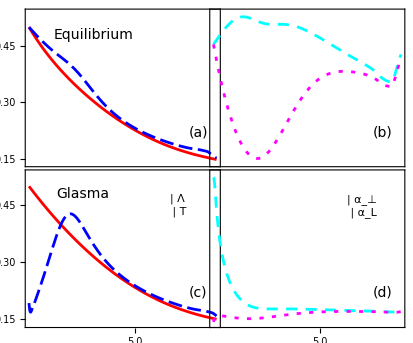
-Graphics-τ (fm/c)

```mathematica
(*Equilibrium*)

TDataRaw=Import[wd<>"/Tplot_vah.dat"];
lambdaDataRaw=Import[wd<>"/lambdaplot_vah.dat"];
axDataRaw=Import[wd<>"/axplot_vah.dat"];
azDataRaw=Import[wd<>"/azplot_vah.dat"];

TData= Take[TDataRaw,{2,Length[TDataRaw]}];
lambdaData= Take[lambdaDataRaw,{2,Length[lambdaDataRaw]}];
axData= Take[axDataRaw,{2,Length[axDataRaw]}];
azData= Take[azDataRaw,{2,Length[azDataRaw]}];

T = Interpolation[TData[[All,{1,2}]]];
lambda = Interpolation[lambdaData[[All,{1,2}]]];
ax = Interpolation[axData[[All,{1,2}]]];
az = Interpolation[azData[[All,{1,2}]]];


(*Glasma*)

TDataRaw2=Import[wd<>"/Tplot_vah2.dat"];
lambdaDataRaw2=Import[wd<>"/lambdaplot_vah2.dat"];
axDataRaw2=Import[wd<>"/axplot_vah2.dat"];
azDataRaw2=Import[wd<>"/azplot_vah2.dat"];

TData2= Take[TDataRaw2,{2,Length[TDataRaw2]}];
lambdaData2= Take[lambdaDataRaw2,{2,Length[lambdaDataRaw2]}];
axData2= Take[axDataRaw2,{2,Length[axDataRaw2]}];
azData2= Take[azDataRaw2,{2,Length[azDataRaw2]}];

T2 = Interpolation[TData2[[All,{1,2}]]];
lambda2 = Interpolation[lambdaData2[[All,{1,2}]]];
ax2 = Interpolation[axData2[[All,{1,2}]]];
az2 = Interpolation[azData2[[All,{1,2}]]];

stylesVAH={Directive[RGBColor[1,0,0],AbsoluteThickness[2]],Directive[RGBColor[1,0,0],AbsoluteThickness[2]],
Directive[RGBColor[1,0,0],AbsoluteThickness[2]],Directive[RGBColor[1,0,0],AbsoluteThickness[2]]};

legendtemp=Panel[Grid[{{Graphics[{Directive[RGBColor[0,0,1],AbsoluteThickness[2],AbsoluteDashing[{10,4}]],Line[{{0,0},{1,0}}]},ImageSize->26.0,AspectRatio->0.2],Style["Λ",FontSize->16,FontFamily->"Calibri"]},
{Graphics[{Directive[RGBColor[1,0,0],AbsoluteThickness[2]],Line[{{0,0},{1,0}}]},ImageSize->26,AspectRatio->0.2],Style["T",FontSize->16,FontFamily->"Calibri"]}}],Background->White];

legendalpha=Panel[Grid[{{Graphics[{Directive[RGBColor[0,1,1],AbsoluteThickness[2],AbsoluteDashing[{8,6}]],Line[{{0,0},{1,0}}]},ImageSize->26,AspectRatio->0.2],Style["α_⊥",FontSize->16,FontFamily->"Calibri"]},
{Graphics[{Directive[RGBColor[1,0,1],AbsoluteThickness[2],AbsoluteDashing[{3,6}]],Line[{{0,0},{1,0}}]},ImageSize->26,AspectRatio->0.2],Style["α_L",FontSize->16,FontFamily->"Calibri"]}}],Background->White];

temp1=LogLinearPlot[{0.197327*T[t],0.197327*lambda[t]},{t,t0,tf},PlotRange->{0.1367,0.54},PlotStyle->{Directive[RGBColor[1,0,0],AbsoluteThickness[2]],Directive[RGBColor[0,0,1],AbsoluteThickness[2],AbsoluteDashing[{10,4}]]},ImageSize->250,Frame->True,Axes->False,FrameTicks->{{All,None},{None,All}},BaseStyle->{FontSize->12},AspectRatio->0.75,Epilog->{Inset[Style["Equilibrium",FontSize->14,FontFamily->"Calibri"],{0.45,0.48}],Inset[Style["(a)",FontSize->14,FontFamily->"Calibri"],{3.4,0.22}]},ImagePadding->{{25,20},{Automatic,Automatic}}];

alpha1=LogLinearPlot[{ax[t],az[t]},{t,t0,tf},PlotRange->{0.52,1.13},PlotStyle->{Directive[RGBColor[0,1,1],AbsoluteThickness[2],AbsoluteDashing[{8,6}]],Directive[RGBColor[1,0,1],AbsoluteThickness[2],AbsoluteDashing[{3,6}]]},ImageSize->250,Frame->True,Axes->False,FrameTicks->{{None,All},{None,All}},BaseStyle->{FontSize->12},AspectRatio->0.75,Epilog->{Inset[Style["(b)",FontSize->14,FontFamily->"Calibri"],{3.4,0.645}]},ImagePadding->{{25,20},{Automatic,Automatic}}];

temp2=LogLinearPlot[{0.197327*T2[t],0.197327*lambda2[t]},{t,t0,tf},PlotRange->{0.1367,0.535},PlotStyle->{Directive[RGBColor[1,0,0],AbsoluteThickness[2]],Directive[RGBColor[0,0,1],AbsoluteThickness[2],AbsoluteDashing[{10,4}]]},ImageSize->250,Frame->True,Axes->False,FrameTicks->{{All,None},{All,None}},BaseStyle->{FontSize->12},AspectRatio->0.75,Epilog->{Inset[Style["Glasma",FontSize->14,FontFamily->"Calibri"],{0.13,0.48}],Inset[legendtemp,{2.8,0.45}],Inset[Style["(c)",FontSize->14,FontFamily->"Calibri"],{3.4,0.22}]},ImagePadding->{{25,20},{Automatic,Automatic}}];

alpha2=LogLinearPlot[{ax2[t],az2[t]},{t,t0,tf},PlotRange->{0,10.5},PlotStyle->{Directive[RGBColor[0,1,1],AbsoluteThickness[2],AbsoluteDashing[{8,6}]],Directive[RGBColor[1,0,1],AbsoluteThickness[2],AbsoluteDashing[{3,6}]]},ImageSize->250,Frame->True,Axes->False,FrameTicks->{{None,All},{All,None}},BaseStyle->{FontSize->12},AspectRatio->0.75,Epilog->{Inset[legendalpha,{2.8,8.2}],Inset[Style["(d)",FontSize->14,FontFamily->"Calibri"],{3.4,2.2}]},ImagePadding->{{25,20},{Automatic,Automatic}}];

anisoplot=Panel[GraphicsGrid[{{temp1,alpha1},{temp2,alpha2}},Spacings->{-49,-22.0}],Style["τ (fm/c)",FontFamily->"Calibri",FontSize->14],{{Bottom,Center}},Appearance->"Frameless",Background->White,ImageSize->{420,325},FrameMargins->0]

Export["aniso.pdf",anisoplot];
```

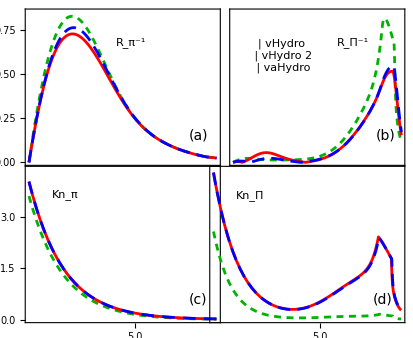
-Graphics-τ (fm/c)

```mathematica
RpiInverseDataRawVH=Import[wd<>"/RpiInvplot_vh.dat"];
RbulkInverseDataRawVH=Import[wd<>"/RbulkInvplot_vh.dat"];

RpiInverseDataVH= Take[RpiInverseDataRawVH,{2,Length[RpiInverseDataRawVH]}];
RbulkInverseDataVH= Take[RbulkInverseDataRawVH,{2,Length[RbulkInverseDataRawVH]}];

RpiInverseVH = Interpolation[RpiInverseDataVH[[All,{1,2}]]];
RbulkInverseVH = Interpolation[RbulkInverseDataVH[[All,{1,2}]]];

(*//////////////////////////////////////////////////////////////*)

RpiInverseDataRawVH2=Import[wd<>"/RpiInvplot_vh_limit.dat"];
RbulkInverseDataRawVH2=Import[wd<>"/RbulkInvplot_vh_limit.dat"];

RpiInverseDataVH2= Take[RpiInverseDataRawVH2,{2,Length[RpiInverseDataRawVH2]}];
RbulkInverseDataVH2= Take[RbulkInverseDataRawVH2,{2,Length[RbulkInverseDataRawVH2]}];

RpiInverseVH2 = Interpolation[RpiInverseDataVH2[[All,{1,2}]]];
RbulkInverseVH2 = Interpolation[RbulkInverseDataVH2[[All,{1,2}]]];

(*//////////////////////////////////////////////////////////////*)

RpiInverseDataRawVAH=Import[wd<>"/RpiInvplot_vah.dat"];
RbulkInverseDataRawVAH=Import[wd<>"/RbulkInvplot_vah.dat"];

RpiInverseDataVAH= Take[RpiInverseDataRawVAH,{2,Length[RpiInverseDataRawVAH]}];
RbulkInverseDataVAH= Take[RbulkInverseDataRawVAH,{2,Length[RbulkInverseDataRawVAH]}];

RpiInverseVAH = Interpolation[RpiInverseDataVAH[[All,{1,2}]]];
RbulkInverseVAH = Interpolation[RbulkInverseDataVAH[[All,{1,2}]]];

(*//////////////////////////////////////////////////////////////*)
(*
RpiInverseDataRawVAHfix1=Import[wd<>"/RpiInvplot_vahfix1.dat"];
RbulkInverseDataRawVAHfix1=Import[wd<>"/RbulkInvplot_vahfix1.dat"];

RpiInverseDataVAHfix1= Take[RpiInverseDataRawVAHfix1,{2,Length[RpiInverseDataRawVAHfix1]}];
RbulkInverseDataVAHfix1= Take[RbulkInverseDataRawVAHfix1,{2,Length[RbulkInverseDataRawVAHfix1]}];

RpiInverseVAHfix1 = Interpolation[RpiInverseDataVAHfix1[[All,{1,2}]]];
RbulkInverseVAHfix1 = Interpolation[RbulkInverseDataVAHfix1[[All,{1,2}]]];*)

taupiDataRawVH=Import[wd<>"/taupiplot_vh.dat"];
taubulkDataRawVH=Import[wd<>"/taubulkplot_vh.dat"];

taupiDataVH= Take[taupiDataRawVH,{2,Length[taupiDataRawVH]}];
taubulkDataVH= Take[taubulkDataRawVH,{2,Length[taubulkDataRawVH]}];

taupiVH = Interpolation[taupiDataVH[[All,{1,2}]]];
taubulkVH = Interpolation[taubulkDataVH[[All,{1,2}]]];

(*//////////////////////////////////////////////////////////////*)

taupiDataRawVH2=Import[wd<>"/taupiplot_vh_limit.dat"];
taubulkDataRawVH2=Import[wd<>"/taubulkplot_vh_limit.dat"];

taupiDataVH2= Take[taupiDataRawVH2,{2,Length[taupiDataRawVH2]}];
taubulkDataVH2= Take[taubulkDataRawVH2,{2,Length[taubulkDataRawVH2]}];

taupiVH2 = Interpolation[taupiDataVH2[[All,{1,2}]]];
taubulkVH2 = Interpolation[taubulkDataVH2[[All,{1,2}]]];

(*//////////////////////////////////////////////////////////////*)

taupiDataRawVAH=Import[wd<>"/taupiplot_vah.dat"];
taubulkDataRawVAH=Import[wd<>"/taubulkplot_vah.dat"];

taupiDataVAH= Take[taupiDataRawVAH,{2,Length[taupiDataRawVAH]}];
taubulkDataVAH= Take[taubulkDataRawVAH,{2,Length[taubulkDataRawVAH]}];

taupiVAH = Interpolation[taupiDataVAH[[All,{1,2}]]];
taubulkVAH = Interpolation[taubulkDataVAH[[All,{1,2}]]];

(*//////////////////////////////////////////////////////////////*)

(*taupiDataRawVAHfix1=Import[wd<>"/taupiplot_vahfix1.dat"];
taubulkDataRawVAHfix1=Import[wd<>"/taubulkplot_vahfix1.dat"];

taupiDataVAHfix1= Take[taupiDataRawVAHfix1,{2,Length[taupiDataRawVAHfix1]}];
taubulkDataVAHfix1= Take[taubulkDataRawVAHfix1,{2,Length[taubulkDataRawVAHfix1]}];

taupiVAHfix1 = Interpolation[taupiDataVAHfix1[[All,{1,2}]]];
taubulkVAHfix1 = Interpolation[taubulkDataVAHfix1[[All,{1,2}]]];*)

legendRbulk=Panel[Style["R_Π^-1",FontSize->16,FontFamily->"Calibri"],Background->White];
legendRpi=Panel[Style["R_π^-1",FontSize->16,FontFamily->"Calibri"],Background->White];
legendKnbulk=Panel[Style["Kn_Π",FontSize->16,FontFamily->"Calibri"],Background->White];
legendKnpi=Panel[Style["Kn_π",FontSize->16,FontFamily->"Calibri"],Background->White];

Rpi=LogLinearPlot[{RpiInverseVH2[t],RpiInverseVAH[t],RpiInverseVH[t]},{t,t0,tf},PlotRange->{-0.00,0.85},PlotStyle->{stylesVH2,stylesVAH,Directive[RGBColor[0,0,1],AbsoluteThickness[2],AbsoluteDashing[{9,5}]]},ImageSize->250,Frame->True,Axes->False,RotateLabel->False,FrameTicks->{{All,None},{None,All}},(*,FrameLabel->{"",Style["R_π^-1",FontSize->16,FontFamily->"Calibri"]},*)BaseStyle->{FontSize->12},AspectRatio->0.75,Epilog->{Inset[Style["(a)",FontSize->14,FontFamily->"Calibri"],{3.4,0.15}],Inset[legendRpi,{1.5,0.68}]},ImagePadding->{{20,25},{Automatic,Automatic}}];

Rbulk=LogLinearPlot[{Abs[RbulkInverseVH2[t]],Abs[RbulkInverseVAH[t]],Abs[RbulkInverseVH[t]]},{t,t0,tf},PlotRange->{-0.00,0.13},PlotStyle->{stylesVH2,stylesVAH,Directive[RGBColor[0,0,1],AbsoluteThickness[2],AbsoluteDashing[{9,5}]]},ImageSize->250,Frame->True,Axes->False,FrameTicks->{{None,All},{None,All}},RotateLabel->False(*FrameLabel->{"","","",Style["R_Π^-1",FontSize->16,FontFamily->"Calibri"]}*),BaseStyle->{FontSize->12},AspectRatio->0.75,Epilog->{Inset[legend1,{0.15,0.092}],Inset[legendRbulk,{2.4,0.104}],Inset[Style["(b)",FontSize->14,FontFamily->"Calibri"],{3.4,0.0229}]},ImagePadding->{{20,25},{Automatic,Automatic}}];

Knpi=LogLinearPlot[{Sqrt[1.5]*taupiVH2[t]/t,Sqrt[1.5]*taupiVAH[t]/t,Sqrt[1.5]*taupiVH[t]/t},{t,t0,tf-0.005},PlotRange->{0,4.4},PlotStyle->{stylesVH2,stylesVAH,Directive[RGBColor[0,0,1],AbsoluteThickness[2],AbsoluteDashing[{9,6}]]},ImageSize->250,Frame->True,Axes->False,FrameTicks->{{All,None},{All,None}},BaseStyle->{FontSize->12},AspectRatio->0.75,Epilog->{Inset[legendKnpi,{-0.35,3.65}],Inset[Style["(c)",FontSize->14,FontFamily->"Calibri"],{3.4,0.58}]},ImagePadding->{{20,25},{Automatic,Automatic}}];

Knbulk=LogLinearPlot[{taubulkVH2[t]/t,taubulkVAH[t]/t,taubulkVH[t]/t},{t,t0,tf-0.005},PlotRange->{0,0.99},PlotStyle->{stylesVH2,stylesVAH,stylesVH},ImageSize->250,Frame->True,Axes->False,FrameTicks->{{None,All},{All,None}},BaseStyle->{FontSize->12},AspectRatio->0.75,Epilog->{Inset[legendKnbulk,{-0.35,0.82}],Inset[Style["(d)",FontSize->14,FontFamily->"Calibri"],{3.4,0.13}]},ImagePadding->{{20,25},{Automatic,Automatic}}];

a3=Panel[GraphicsGrid[{{Rpi,Rbulk},{Knpi,Knbulk}},Spacings->{-49,-24.3}],Style["τ (fm/c)",FontFamily->"Calibri",FontSize->14],{{Bottom,Center}},Background->White,ImageSize->{420,325},FrameMargins->0]

Export["compare_validity.pdf",a3];
```